On the last notebook I derived the model for the far field imaging, i.e.
	Y = (R.F.(M.X)ᵀ)ᵀ
But the dimension of Y is (k, m) and X is (n,n). I encountered problem when taking the pseudoinverse of the matrix.

This time I wanted to search for a form where:
	Y = S.X
but Y and X  is a vector, i.e. dim@Y=(m*k,1) and dim@X=(n,1)

Based on the numerical trial in the following I found that:
	(S=Outer[Times,M,R.F,1,1]//Flatten[#,1]&)

Therefore the requirement would be to find M, such that MatrixRank@S = Dim@X
	i.e. in this case if MatrixRank@S == 4, then X = PseudoInverse@S.Y

(0.875
0.625
0.125
0.375)

(0.730989
0.567426
0.351579
0.824175)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2)

(5/6 | 1/6 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 1/6 | 5/6)

(0.25+0. ⅈ | 0.208333+0.0416667 ⅈ | 0.166667+0. ⅈ | 0.208333-0.0416667 ⅈ
0.25+0. ⅈ | -0.125+0.125 ⅈ | 0.+0. ⅈ | -0.125-0.125 ⅈ
0.25+0. ⅈ | -0.0416667-0.208333 ⅈ | -0.166667+0. ⅈ | -0.0416667+0.208333 ⅈ
0.25+0. ⅈ | 0.208333+0.0416667 ⅈ | -0.166667+0. ⅈ | -0.208333+0.0416667 ⅈ
0.25+0. ⅈ | -0.125+0.125 ⅈ | 0.+0. ⅈ | 0.125+0.125 ⅈ
0.25+0. ⅈ | -0.0416667-0.208333 ⅈ | 0.166667+0. ⅈ | 0.0416667-0.208333 ⅈ
0.25+0. ⅈ | -0.208333-0.0416667 ⅈ | -0.166667+0. ⅈ | 0.208333-0.0416667 ⅈ
0.25+0. ⅈ | 0.125-0.125 ⅈ | 0.+0. ⅈ | -0.125-0.125 ⅈ
0.25+0. ⅈ | 0.0416667+0.208333 ⅈ | 0.166667+0. ⅈ | -0.0416667+0.208333 ⅈ
0.25+0. ⅈ | -0.208333-0.0416667 ⅈ | 0.166667+0. ⅈ | -0.208333+0.0416667 ⅈ
0.25+0. ⅈ | 0.125-0.125 ⅈ | 0.+0. ⅈ | 0.125+0.125 ⅈ
0.25+0. ⅈ | 0.0416667+0.208333 ⅈ | -0.166667+0. ⅈ | 0.0416667-0.208333 ⅈ)

4

(0.53126-0.0106979 ⅈ
0.00879715-0.0320936 ⅈ
0.0661674+0.0534893 ⅈ
0.0706615+0.0579833 ⅈ
0.214841+0.17395 ⅈ
0.252041-0.289917 ⅈ
0.17764-0.0579833 ⅈ
0.150654-0.17395 ⅈ
0.230646+0.289917 ⅈ
-0.0485731+0.0106979 ⅈ
0.356697+0.0320936 ⅈ
0.182134-0.0534893 ⅈ)

(0.787265+3.46945×10^-18 ⅈ
0.55615-0.027907 ⅈ
0.382362-1.11022×10^-16 ⅈ
0.839968+0.036332 ⅈ)

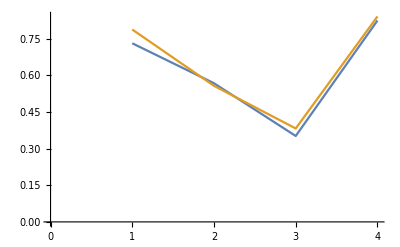

```mathematica
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm//N
(X = RandomReal[1,4])//MatrixForm
(H =DiscreteHadamardTransform/@IdentityMatrix[4])//MatrixForm
(R = ArrayResample[#,{3},"Bin",Resampling->"Linear"]&/@IdentityMatrix[4]//Transpose)//MatrixForm
(*(R = ({{1/4, 1/4, 1/4, 1/4}}))//MatrixForm*)
(M = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm;
(F=Fourier/@IdentityMatrix[4])//MatrixForm;
(S=Outer[Times,M,R.F,1,1]//Flatten[#,1]&)//MatrixForm
(MatrixRank@S)
(Y=(S.X))//MatrixForm 
(noise = Table[RandomReal[{-0.05,0.05}],{Dimensions[Y][[1]]}])//MatrixForm;
(Y= Y+noise)//MatrixForm;
(rX = PseudoInverse@S.Y)//MatrixForm//N
ListLinePlot[{X,Abs@rX}]
```

The following section will discuss the idea and check the consistency with the previous model.

# Near field trial

We suppose each measurement will capture several y, in this case m=3.
The idea is to take outer product of  the rows of R with the mask M, i.e. first mask will fill y_1, y_2, y_3,
 and so on.

```mathematica
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm//N;
(R = ArrayResample[#,{3},"Bin",Resampling->"Linear"]&/@IdentityMatrix[4]//Transpose)//MatrixForm;
(M = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm;
(F=Fourier/@IdentityMatrix[4])//MatrixForm;

(Y=(R.(M.DiagonalMatrix@X)ᵀ)ᵀ)//MatrixForm//N
(S=Outer[Times,M,R,1,1]//Flatten[#,1]&)//MatrixForm;
(Yf=S.X//ArrayReshape[#,Dimensions@Y]&)//MatrixForm//N
Yf==Y
```

(0.416667 | 0.1875 | 0.166667
0.416667 | 0.125 | -0.166667
0.3125 | -0.1875 | 0.145833
0.3125 | -0.125 | -0.145833)

(0.416667 | 0.1875 | 0.166667
0.416667 | 0.125 | -0.166667
0.3125 | -0.1875 | 0.145833
0.3125 | -0.125 | -0.145833)

True

# Far field trial
Then note (A) and (B), i.e. (A) is the full model I described on the last notebook.
We just substitute R on the above cell with R.F to get the correct form of S for far field.

```mathematica
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm//N;
(R = ArrayResample[#,{3},"Bin",Resampling->"Linear"]&/@IdentityMatrix[4]//Transpose)//MatrixForm;
(M = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm;
(F=Fourier/@IdentityMatrix[4])//MatrixForm;

(*A*) (Y=(R.F.(M.DiagonalMatrix@X)ᵀ)ᵀ)//MatrixForm//N
(*B*) (S=Outer[Times,M,R.F,1,1]//Flatten[#,1]&)//MatrixForm;
(Yf=S.X//ArrayReshape[#,Dimensions@Y]&)//MatrixForm//N
Yf==Y
```

(0.447917+0.0104167 ⅈ | 0.09375+0.03125 ⅈ | 0.15625-0.0520833 ⅈ
0.25+0.0416667 ⅈ | 0.1875+0.125 ⅈ | 0.229167-0.208333 ⅈ
0.145833-0.0416667 ⅈ | 0.25-0.125 ⅈ | 0.25+0.208333 ⅈ
0.03125-0.0104167 ⅈ | 0.34375-0.03125 ⅈ | 0.239583+0.0520833 ⅈ)

(0.447917+0.0104167 ⅈ | 0.09375+0.03125 ⅈ | 0.15625-0.0520833 ⅈ
0.25+0.0416667 ⅈ | 0.1875+0.125 ⅈ | 0.229167-0.208333 ⅈ
0.145833-0.0416667 ⅈ | 0.25-0.125 ⅈ | 0.25+0.208333 ⅈ
0.03125-0.0104167 ⅈ | 0.34375-0.03125 ⅈ | 0.239583+0.0520833 ⅈ)

True

```mathematica
Clear[M]
M = Table[Subscript[m, i,j],{i,4},{j,4}];
(S=Outer[Times,M,R,1,1]//Flatten[#,1]&)//MatrixForm
F.IdentityMatrix[4]//MatrixForm
```

((5 m_(1,1))/6 | (m_(1,2))/6 | 0 | 0
0 | (m_(1,2))/2 | (m_(1,3))/2 | 0
0 | 0 | (m_(1,3))/6 | (5 m_(1,4))/6
(5 m_(2,1))/6 | (m_(2,2))/6 | 0 | 0
0 | (m_(2,2))/2 | (m_(2,3))/2 | 0
0 | 0 | (m_(2,3))/6 | (5 m_(2,4))/6
(5 m_(3,1))/6 | (m_(3,2))/6 | 0 | 0
0 | (m_(3,2))/2 | (m_(3,3))/2 | 0
0 | 0 | (m_(3,3))/6 | (5 m_(3,4))/6
(5 m_(4,1))/6 | (m_(4,2))/6 | 0 | 0
0 | (m_(4,2))/2 | (m_(4,3))/2 | 0
0 | 0 | (m_(4,3))/6 | (5 m_(4,4))/6)

(0.5+0. ⅈ | 0.5+0. ⅈ | 0.5+0. ⅈ | 0.5+0. ⅈ
0.5+0. ⅈ | 0.+0.5 ⅈ | -0.5+0. ⅈ | 0.-0.5 ⅈ
0.5+0. ⅈ | -0.5+0. ⅈ | 0.5+0. ⅈ | -0.5+0. ⅈ
0.5+0. ⅈ | 0.-0.5 ⅈ | -0.5+0. ⅈ | 0.+0.5 ⅈ)